# Memoization

## Introduction

In this lesson, we’ll look at using a programming method called memoization in Mathematica. For more information about memoization, see https://en.wikipedia.org/wiki/Memoization.  The idea behind memoization is to cache the output of a function associated with a given input in memory so that if a user wishes to later evaluate that function at the same input, to computer can look up the cached value of the function instead of recomputing the result. This can be especially useful when function calls are expensive (i.e. take a lot of processing time) or recursive. If you are familiar with the adage “time is money”, then the work expensive makes good sense in this context. Let’s look at a recursive implementation of the Fibonacci numbers in Mathematica.

## Fibonacci numbers - naive approach

We’ll define a function f recursively to generate the nth Fibonacci number.

```mathematica
f[0] = 1; (* first initial condition *)
f[1] = 1; (* second intitial condition *)
f[n_]:=f[n-1] + f[n-2];  (* for n ≥ 2 *)
```

What happens if we evaluate f[15]? In order to evaluate the expression, Mathematica needs to evaluate both f[14] and f[13]. However, to evaluate f[14], Mathematica needs to evaluate f[13] and f[12]. Already, we have inefficiency, as we’re evaluating f[13] twice! If f[13] takes time to evaluate, calling it twice is really a waste of time. In fact, other values are called even more. Let’s investigate how many times f is called at each input. Mathematica has a command called Trace (check it out using ?Trace) that will return a list of every expression that is evaluated in the evaluation of the input to Trace. Get a feel for the function by evaluating small cases.

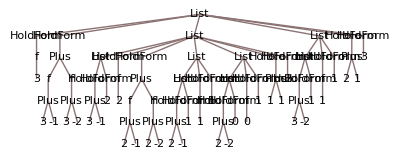

```mathematica
Trace[f[3]]//TreeForm
```

However, we aren’t interested in every single expression that is evaluated, we’re interested in calls to f. This can be accomplished by giving Trace another argument.

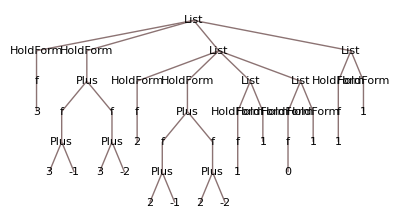

```mathematica
Trace[f[3],f]//TreeForm
```

This is closer, but not quite what we want, because this list also contains the expressions obtained before simplifying differences of integers. What we really want to track is calls to the function f with a single expression as input. This can be accomplished using patterns.

```mathematica
Trace[f[3],f[_]]
```

{f[3],{f[2],{f[1]},{f[0]}},{f[1]}}
 |  |  |  |

Now, we can flatten the list and count the elements.

```mathematica
Counts[Flatten[Trace[f[15],f[_]]]]
```

<|f[15]→1,f[14]→1,f[13]→2,f[12]→3,f[11]→5,f[10]→8,f[9]→13,f[8]→21,f[7]→34,f[6]→55,f[5]→89,f[4]→144,f[3]→233,f[2]→377,f[1]→610,f[0]→377|>
 |  |  |  |

This is already obviously remarkably inefficient. We’ve called f[3] three hundred and seventy seven times. A human would perform this calculation once. This problem scales wildly as the input increases as well. We can look at how long a computation takes with the command AbsoluteTiming.

```mathematica
f[15]//AbsoluteTiming
```

{0.0015614,987}

```mathematica
Fibonacci[16]//AbsoluteTiming
```

{2.8×10^-6,987}

Even here we can see orders of magnitude in the difference in timing. Our function takes 10^-3 seconds and the built-in takes on the order of 10^-6. Let’s try a bigger number.

```mathematica
AbsoluteTiming[f[35]]
```

{22.1359,14930352}

```mathematica
AbsoluteTiming[Fibonacci[36]]
```

{2.8×10^-6,14930352}

Our function took 22 seconds to produce an answer that the build in function produced in about a millionth of a second. If we look at the trace, we can see why. (I do not recommend that you try this yourself. It took five minutes to run on my rather powerful computer.)

```mathematica
Trace[f[35], f[_]]
```

{f[35],{1},{f[33],{f[32],1,1},{f[31],{f[30],1,1},{f[29],{f[28],1,1},{f[27],{f[26],{f[25],1,1},1},{f[25],{f[24],1,{f[22],1,1}},{f[23],1,{f[21],{f[20],1,1},1}}}}}}}}
 |  |  |  |

```mathematica
Counts[Flatten[Out[120]]]
```

<|f[35]→1,f[34]→1,f[33]→2,f[32]→3,f[31]→5,f[30]→8,f[29]→13,f[28]→21,f[27]→34,f[26]→55,f[25]→89,f[24]→144,f[23]→233,f[22]→377,f[21]→610,6,f[14]→17711,f[13]→28657,f[12]→46368,f[11]→75025,f[10]→121393,f[9]→196418,f[8]→317811,f[7]→514229,f[6]→832040,f[5]→1346269,f[4]→2178309,f[3]→3524578,f[2]→5702887,f[1]→9227465,f[0]→5702887|>
 |  |  |  |

Of note is that f[2] was computed six million times to produce the 35th Fibonacci number.

## Memoization

You should notice that in the definition of our function, we explicitly defined f[0]=1. So evaluation of f[0] is easy, because Mathematica sees that the value is stored in memory and it returns that value instead of trying to compute it. In general, Mathematica will try to choose the definition of f that is most specific to the input given. All three of the definitions above involving f are referred to as the downvalues of f. These can be seen using the DownValues command.

```mathematica
DownValues[f]
```

{HoldPattern[f[0]]:>1,HoldPattern[f[1]]:>1,HoldPattern[f[n_]]:>f[n-1]+f[n-2]}
 |  |  |  |

What we would like to do is have Mathematica explicitly define the value of f when it performs an evaluation of f. This can be accomplished by setting the delayed rule for f to be an assignment statement. This means that f is capable of creating new downvalues when evaluated. Additionally, the output from evaluating an assignment statement is the value of the assigned variable, so the following definition of f works exactly the way that we wish.

```mathematica
f[n_]:=f[n]=f[n-1] + f[n-2]
```

Let’s call f[5] and look at the downvalues.

```mathematica
f[5]
```

8

```mathematica
DownValues[f]
```

{HoldPattern[f[0]]:>1,HoldPattern[f[1]]:>1,HoldPattern[f[2]]:>2,HoldPattern[f[3]]:>3,HoldPattern[f[4]]:>5,HoldPattern[f[5]]:>8,HoldPattern[f[n_]]:>(f[n]=f[n-1]+f[n-2])}
 |  |  |  |

Notice that Mathematica now has downvalues stored for f for input values 0, 1, 2, 3, 4, and 5. There are no downvalues stored for larger n because we haven’t yet asked Mathematica to evaluate anything higher. Let us now use our new definition to compute f[35].

```mathematica
f[35]//AbsoluteTiming
```

{0.0001819,14930352}

```mathematica
22/.0001819
```

120946.

Our new implementation computed f[35] approximately 120,000 times faster than the naive approach we took above. Of course, this wasn’t “free” - we’ve traded memory (storing the numbers) for speed. Computers used to have tight limits on available memory that made this a real tradeoff in many situations. Fortunately, in the era of cheap memory and large hard drives, this is often not a concern for modern mathematicians. Use memoization to complete the exercises below.

## Exercises

#### Exercise 1

The Pell numbers are defined by P_0=0, P_1= 1 and P_n= 2 P_(n-1)+P_(n-2) for n ≥ 2. 
1. Write a recursive function called Pell[n_] that returns P_n.

2. Compute P[100].

3. Verify that

P_n= ((1 + √2)^n- (1 - √2)^n)/(2 √2)

for 0 ≤n ≤ 100 (this statement actually holds for all nonnegative n).

#### Exercise 2

The k step Fibonacci numbers are defined by F_k(n) = 0 for n ≤ 0, F_k(1) = 1, and for n ≥ 1 the formula

F_k(n)=∑_(i=1)^k F_k(n-i).

1. Write a recursive function called Fib[n_, k_] that returns F_k(n). Defining Fib to be zero whenever n<0 can be accomplished using pattern matching in the function definition.

2. Compute F_7(80), the 80th 7-step Fibonacci number.

#### Exercise 3

The probabilists’ Hermite polynomials are defined by the formula

H_n(x) = Piecewise[{{1,, n = 0;}, {x,, n = 1;}, {x H_(n-1)(x) - ⅆ/ⅆx H_(n-1)(x),, n ≥ 2.}}]

1. Write a recursive function called Hermite[n_] that returns H_n(x) expanded as a sum of powers of x. (See Expand.)

2. Compute H_90(x).

3. Verify that the coefficient of t^n in the power series expansion of ⅇ^(xt - t^2/2) about t = 0 is equal to (H_n(x))/(n!)for 1≤ n ≤ 20. (Hint: To expand a function as a power series, check out Series. The functions CoefficientList and SeriesCoefficient may also come in handy.

#### Exercise 4

A Motzkin path of length n is a line segment P_0 P_1 P_2... P_n starting at the origin and ending at (n, 0) which never dips below the x-axis satisfying the additional condition that P_(i+1) must equal P_i+(1,1), P_i+(1, -1), or P_i + (1,0). In other words, P_(i+1) lies one unit to the right of P_i and is either one unit above or at the same height as P_i or is one unit lower than P_i (so long as P_i is not on the x-axis). By convention, (0,0) is considered a Motzkin path of length 0. We will store Motzkin paths in Mathematica as a list of points. For example, {(0,0}, {1,1}, {2,0}} is a Motzkin path of length 2.

1. Write a function called DrawPath[P_] that will draw a path in the xy-plane corresponding to the list of points P of length n. Fix the viewing window so that 0 ≤ x ≤ n and -1 ≤ y ≤ n/2. (This can be done in a single line).

2. Evaluate

```mathematica
DrawPath[{{0,0}, {1, 0}, {2,1}, {3,2},{4,2}, {5, 1}, {6,2}, {7,1}, {8,0}}]
```

3. Every Motzkin path of length n is either a Motzkin path of length n-1 followed by (n,0) or a Motzkin path of length i followed by a Motzkin path of length n - i - 2 that has been shifted i+1 units to the right and one unit up followed by (n,0) for some 0 ≤ i ≤ n-2. Using this fact, write a recursive function MotzkinPaths[n_] that produces a list of all Motzkin paths of length n as sequences of points. To get you started, begin with

```mathematica
MotzkinPaths[0]:= {{0,0}};
MotzkinPaths[1]:={{0,0}, {1, 0}};
```

Below is an image containing the correct output for

```mathematica
GraphicsGrid[{DrawPath/@MotzkinPaths[3]}];
```

{-Graphics-}

Use this to verify that your function is working correctly in this case. This exercise is challenging! To try to keep things a little more manageable, try to break the cases up into separate functions and try to get them working piece by piece. For example, first write a function that appends (n,0) to all Motzkin paths of length n.  Following this, write a function of i that creates all the paths as described above for this specific i. Try going through the process of creating the two Motzkin paths of length 2 on your own and then try to generalize. It is possible to get a version working using only Join, Append, Flatten, Functions, Outer, Map,  and Range.

4. Display all the Motzkin paths of length 5 with the command

```mathematica
Map[DrawPath, MotzkinPaths[5]]
```

5. Produce a random Motzkin path of length 13 with the command

```mathematica
DrawPath[RandomChoice[MotzkinPaths[13]]]
```

6. Determine the number of Motzkin paths of length 14 by evaluating

```mathematica
Length[MotzkinPaths[14]]
```

7. Use AbsoluteTiming to determine how long it takes Mathematica to evaluate the above command.

8. Clear your definition of MotzkinPaths from memory and create a non-memoized version of this function. How long does it take Mathematica to evaluate the command from part 6? How many times faster is the memoized version than the non-memoized version in this case?